From Lab 5: Nonlinear pendulum

{{ϕ→InterpolatingFunction[…]}}

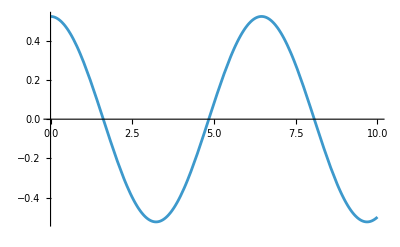

```mathematica
g = 9.81;
l = 10;
ω = Sqrt[g/l];

sol=NDSolve[{ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ'[0]==0,ϕ[0]==30 Degree},ϕ,{t,0,10}]
Plot[ϕ[x]/. sol,{x,0,10}]
```

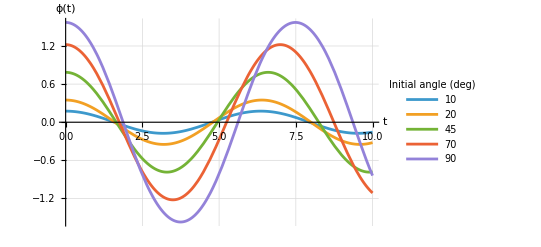

```mathematica
Clear[g,l,ω,ϕ,t,a,s]
g=9.81;
l=10;
ω=Sqrt[g/l];

angles={10,20,45,70,90};
s=Table[NDSolveValue[{ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ'[0]==0,ϕ[0]==a Degree},ϕ,{t,0,10}],{a,angles}];
Plot[Evaluate@Table[s[[i]][t],{i,Length[angles]}],{t,0,10},PlotLegends->Placed[LineLegend[Style[#,12]&/@angles,LegendLabel->"Initial angle (deg)"],Right],AxesLabel->{"t","ϕ(t)"},PlotRange->All,GridLines->Automatic]
```

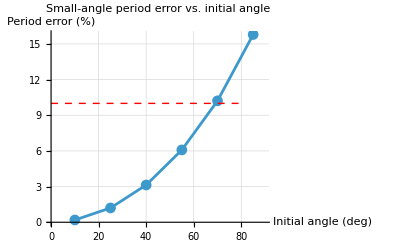

```mathematica
Angles=Range[10,85,15];
Solutions=Table[NDSolveValue[{ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ'[0]==0,ϕ[0]==angle Degree},ϕ,{t,0,10}],{angle,Angles}];
smallAngleApprox=2 Pi/ω;
quarterPeriods=Table[t/. FindRoot[Solutions[[i]][t]==0,{t,0,3/ω}],{i,Length[Angles]}];
simulatedPeriods=4 quarterPeriods;
periodErrorPercent=100 Abs[(simulatedPeriods-smallAngleApprox)/smallAngleApprox];
firstAtTenPercent=First@Select[Transpose[{Angles,periodErrorPercent}],Last[#]>=10&];
thresholdAngle=180/Pi (θ/. FindRoot[2 EllipticK[Sin[θ/2]^2]/Pi==1.1,{θ,1.2}]);
ListLinePlot[Transpose[{Angles,periodErrorPercent}],PlotMarkers->Automatic,PlotRange->{{0,90},{0,All}},AxesLabel->{"Initial angle (deg)","Period error (%)"},PlotLabel->"Small-angle period error vs. initial angle",GridLines->Automatic,Epilog->{Red,Dashed,Line[{{0,10},{80,10}}]}]
```

Mass does not affect the dynamics of motion as it is canceled out in the end.